# Drugs

## Isolating the Drugs

```mathematica
Drugs=EntityList[EntityClass["Chemical","Drugs"]];
```

```mathematica
missingACs2=Select[Drugs,MissingQ[#["AtomCount"]]&];
```

```mathematica
drugsWithAc=Complement[Drugs,missingACs2];
```

```mathematica
Length[drugsWithAc]
```

4475

```mathematica
missingBps2=Select[drugsWithAc,MissingQ[#["BoilingPoint"]]&];
```

```mathematica
drugsWithBP=Complement[drugsWithAc,missingBps2];
```

```mathematica
Length[drugsWithBP]
```

682

```mathematica
drugMolecules=ParallelMap[Molecule,drugsWithBP];
```

## Descriptors

```mathematica
SmilesDrugs=ParallelMap[#["SMILES"]&,drugsWithBP];
```

```mathematica
BpDrugs=ParallelMap[#["BoilingPoint"]&,drugsWithBP];
```

```mathematica
acDrugs=ParallelMap[#["AtomCount"]&,drugsWithBP];
```

```mathematica
mmDrugs=ParallelMap[MoleculeValue[#,"MolecularMass"]&,drugMolecules];
```

```mathematica
rgDrugs=ParallelMap[MoleculeValue[#,"RadiusOfGyration"]&,drugMolecules];
```

```mathematica
cnDrugs=ParallelMap[MoleculeValue[#,"HeteroatomCount"]&,drugMolecules];
```

```mathematica
KhasDrugs=ParallelMap[MoleculeValue[#,"KierHallAlphaShape"]&,drugMolecules];
```

```mathematica
LaSaDrugs=ParallelMap[MoleculeValue[#,"LabuteApproximateSurfaceArea"]&,drugMolecules];
```

```mathematica
SasDrugs=ParallelMap[MoleculeValue[#,"SyntheticAccessibilityScore"]&,drugMolecules];
```

```mathematica
PobfDrugs=ParallelMap[MoleculeValue[#,"PlaneOfBestFitDistance"]&,drugMolecules];
```

## Making a dataset

```mathematica
measurementsDrugs=Transpose[{SmilesDrugs,QuantityMagnitude[BpDrugs],QuantityMagnitude[acDrugs],QuantityMagnitude[mmDrugs],QuantityMagnitude[rgDrugs],QuantityMagnitude[cnDrugs],QuantityMagnitude[KhasDrugs],QuantityMagnitude[LaSaDrugs],QuantityMagnitude[SasDrugs],QuantityMagnitude[PobfDrugs]}];
```

```mathematica
variableNamesDrugs={"Smiles","Bp","Ac","Mm","Rg","Cn","Khas","LaSa","Sas","Pobf"};
```

```mathematica
drugData=ResourceFunction["DatasetWithHeaders"][measurementsDrugs,variableNamesDrugs]
```

```mathematica
dataFitting2=Values[Normal[drugData[All,{"Bp","Ac","Mm","Rg","Cn","Khas","LaSa","Sas","Pobf"}]]];
```

```mathematica
Graph2=ResourceFunction["PairwiseScatterPlot"][dataFitting2,"DataLabels"-> {"Bp","Ac","Mm","Rg","Cn","Khas","LaSa","Sas","Pobf"}]
```

-Graphics-

## Pearson Correlation

```mathematica
PearsonCorrelationTest[BpDrugs,LaSaDrugs,"TestStatistic"]
```

0.236214

```mathematica
PearsonCorrelationTest[acDrugs,LaSaDrugs,"TestStatistic"]
```

0.973624

```mathematica
PearsonCorrelationTest[mmDrugs,LaSaDrugs,"TestStatistic"]
```

0.929536

```mathematica
PearsonCorrelationTest[rgDrugs,LaSaDrugs,"TestStatistic"]
```

0.843196

```mathematica
PearsonCorrelationTest[cnDrugs,LaSaDrugs,"TestStatistic"]
```

0.408882

```mathematica
PearsonCorrelationTest[KhasDrugs,LaSaDrugs,"TestStatistic"]
```

-0.47856

```mathematica
PearsonCorrelationTest[SasDrugs,LaSaDrugs,"TestStatistic"]
```

0.177282

```mathematica
PearsonCorrelationTest[PobfDrugs,LaSaDrugs,"TestStatistic"]
```

0.691775

## Machine Learning Functions

```mathematica
predictorVars2=Normal@Values@drugData[All,{"Smiles","Ac","Mm","Rg","Pobf"}];
```

```mathematica
outputValue2=Normal@drugData[All,"LaSa"];
```

```mathematica
fullDataSetPredict2=MapThread[Rule,{predictorVars2,outputValue2}];
```

```mathematica
fullTrainingSet2=RandomSample[fullDataSetPredict2,Round[0.8*Length[fullDataSetPredict2]]];
```

```mathematica
fullTestingSet2=Complement[fullDataSetPredict2,fullTrainingSet2];
```

```mathematica
trainingSet2Values=Rest/@Keys[fullTrainingSet2];
```

```mathematica
trainingSet2Output=Values[fullTrainingSet2];
```

```mathematica
trainingSet2=MapThread[Rule,{trainingSet2Values,trainingSet2Output}];
```

```mathematica
testingSet2Values=Rest/@Keys[fullTestingSet2];
```

```mathematica
testingSet2Output=Values[fullTestingSet2];
```

```mathematica
testingSet2=MapThread[Rule,{testingSet2Values,testingSet2Output}];
```

#### Linear Regression

```mathematica
pred1p=Predict[trainingSet2, Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
pm1p=PredictorMeasurements[pred1p,testingSet2]
```

PredictorMeasurementsObject[…]

```mathematica
Dataset[AssociationMap[pm1p[#,ComputeUncertainty->True]&,{"StandardDeviation","RSquared","EvaluationTime"}]]
```

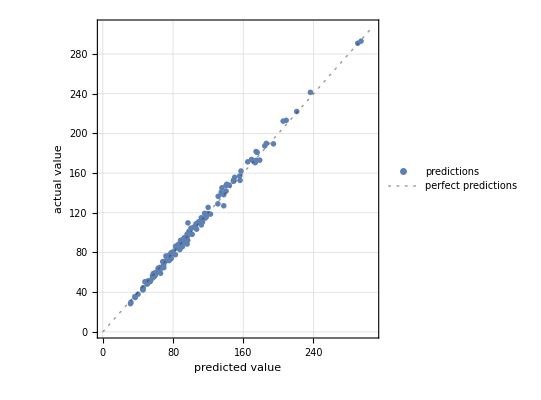

```mathematica
PredictorMeasurements[pred1p,testingSet2,"ComparisonPlot"]
```

#### Neural Network

```mathematica
pred2p=Predict[trainingSet2,Method->"NeuralNetwork"]
```

PredictorFunction[…]

```mathematica
pm2p=PredictorMeasurements[pred2p,testingSet2]
```

PredictorMeasurementsObject[…]

```mathematica
Dataset[AssociationMap[pm2p[#,ComputeUncertainty->True]&,{"StandardDeviation","RSquared","EvaluationTime"}]]
```

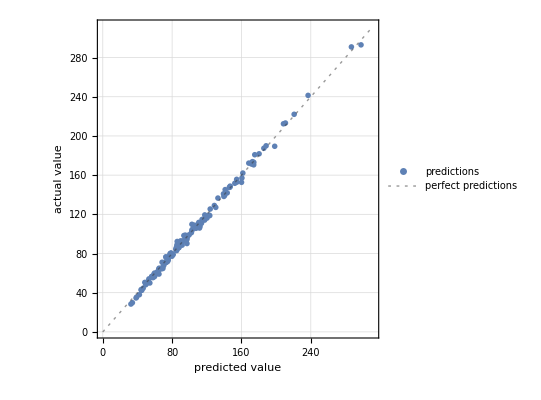

```mathematica
y=PredictorMeasurements[pred2p,testingSet2,"ComparisonPlot"]
```

#### Gradient Boosted Trees

```mathematica
pred3p=Predict[trainingSet2,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

```mathematica
pm3p=PredictorMeasurements[pred3p,testingSet2]
```

PredictorMeasurementsObject[…]

```mathematica
Dataset[AssociationMap[pm3p[#,ComputeUncertainty->True]&,{"StandardDeviation","RSquared","EvaluationTime"}]]
```

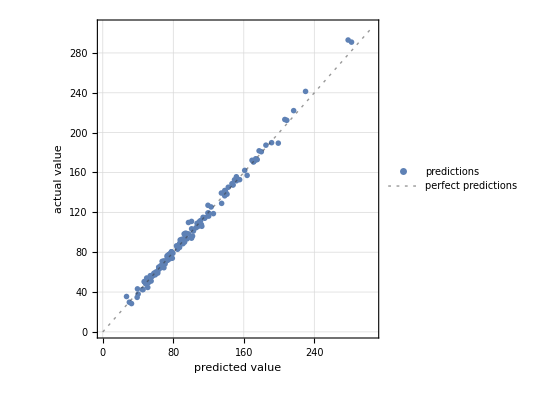

```mathematica
PredictorMeasurements[pred3p,testingSet2,"ComparisonPlot"]
```

#### Random Forest

```mathematica
pred4p=Predict[trainingSet2,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
pm4p=PredictorMeasurements[pred4p,testingSet2]
```

PredictorMeasurementsObject[…]

```mathematica
Dataset[AssociationMap[pm4p[#,ComputeUncertainty->True]&,{"StandardDeviation","RSquared","EvaluationTime"}]]
```

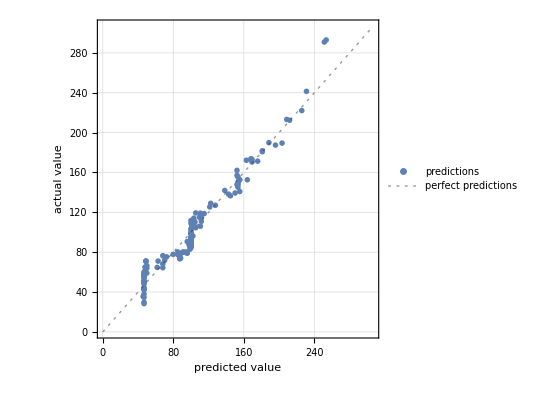

```mathematica
PredictorMeasurements[pred4p,testingSet2,"ComparisonPlot"]
```

#### Decision Tree

```mathematica
pred5p=Predict[trainingSet2,Method->"DecisionTree"]
```

PredictorFunction[…]

```mathematica
pm5p=PredictorMeasurements[pred5p,testingSet2]
```

PredictorMeasurementsObject[…]

```mathematica
Dataset[AssociationMap[pm5p[#,ComputeUncertainty->True]&,{"StandardDeviation","RSquared","EvaluationTime"}]]
```

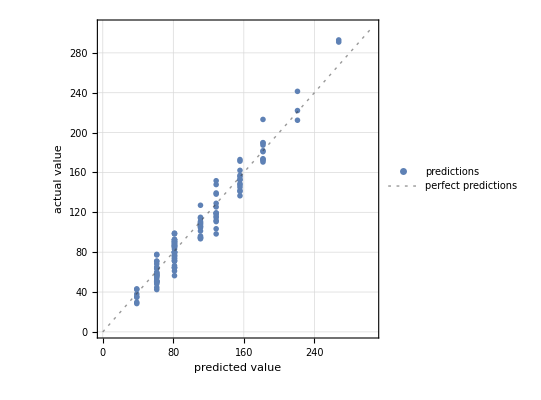

```mathematica
PredictorMeasurements[pred5p,testingSet2,"ComparisonPlot"]
```

### Gaussian Process

```mathematica
pred6p=Predict[trainingSet2,Method->"GaussianProcess"]
```

PredictorFunction[…]

```mathematica
pm6p=PredictorMeasurements[pred6p,testingSet2]
```

PredictorMeasurementsObject[…]

```mathematica
Dataset[AssociationMap[pm6p[#,ComputeUncertainty->True]&,{"StandardDeviation","RSquared","EvaluationTime"}]]
```

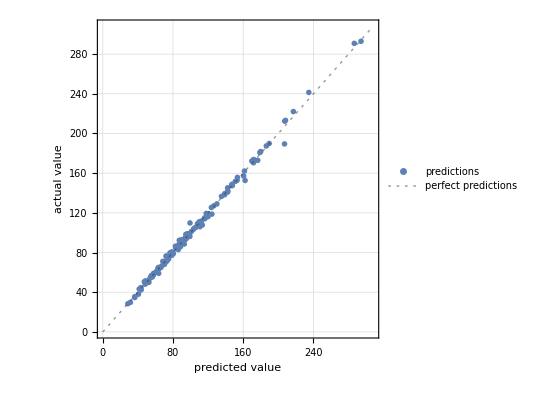

```mathematica
PredictorMeasurements[pred6p,testingSet2,"ComparisonPlot"]
```

## Predicting Citalopram’s Molecular Surface Area

```mathematica
fullTestingSet2[[128]]
```

{CN(C)CCCC1(C2=C(CO1)C=C(C=C2)C#N)C3=CC=C(C=C3)F,45,324.399,3.93421,1.17359}→171.338

```mathematica
pred2p[Keys@testingSet2[[128]]]
```

171.59

```mathematica
ChemicalData["Citalopram","MoleculePlot"]
```

-Graphics3D-

```mathematica
ChemicalData["Citalopram","SpaceFillingMoleculePlot"]
```

-Graphics3D-

## Manipulate App

```mathematica
pred2p[{45,324.399,3.93421,1.17359}]
```

171.59

```mathematica
pred2p[{{100,100,100,0},{20,10,100,3},{25,23,40,0.2},{43,129,10,33},{12,30,52,0.8},{64,12,150,0},{50,670,1,0.7},{4,30,10,0.9},{54,264,00,5},{10,10,100,2},{45,23,45,0}}]
```

{1203.32,1224.88,548.957,762.331,697.138,1826.79,207.832,153.031,188.681,1254.35,593.033}

```mathematica
drugsCalc=Framed[Manipulate[ToString[pred2p[{atomCount,molecularMass,radiusOfGyration,planeOfBestFitDistance}]],Style["Drugs Surface Area Calculator",14,Bold,Orange],Delimiter,{{atomCount,45,"Atom Count"},2,120},{{molecularMass,324.399, "Molecular Mass"},26.038,822.942},{{radiusOfGyration,3.9342068720153947,"Radius of Gyration"},0.22462,10.7024},{{planeOfBestFitDistance,1.173585005030939,"Plane of Best Fit Distance"},0.,1.22643},ControlType->InputField,SaveDefinitions->True,ControlPlacement->Left,Paneled->False],FrameMargins->
5,Background->Lighter[Gray,0.9],RoundingRadius->7.5]
```

```mathematica
pred2p
```

PredictorFunction[…]

```mathematica
Information[pred2p]
```

Predictor information
Data type | Mixed (number: 4)
Standard deviation | 9.62 ± 1.8
Method | NeuralNetwork
Single evaluation time | 2.27 ms/example
Batch evaluation speed | 9.43 examples/ms
Loss | 3.29 ± 0.072
Model memory | 305. kB
Training examples used | 548 examples
Training time | 31.3 s
 |